```mathematica
SetDirectory[NotebookDirectory[]];
AOList=BinaryReadList["AO.float", "Real32"];
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1395222,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
 |  |  |  |

```mathematica
AOListInt= Map[Function[x,Round[1000.0*x]],AOList];
```

```mathematica
histo=HistogramList[AOListInt,{10}]
Length[histo[[1]]]
Length[histo[[2]]]
```

{{-10,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000,1010},{0,248365,1634,1397,1227,1497,2539,3022,1078,803,616,666,875,958,543,855,1077,513,1056,3521,666,619,626,595,642,779,586,382,788,611,580,577,818,242,933,1148,3068,739,421,686,621,422,524,672,662,1042,978,510,468,560,529,563,608,878,2106,3802,1020,1050,568,716,535,571,670,819,761,901,661,904,701,278,1115,1068,1912,4025,942,527,624,773,469,944,384,1192,1499,527,1080,598,678,1138,5966,867,813,1166,1098,830,1811,1325,1072,1857,6950,1699,2648,1034847}}

103

102

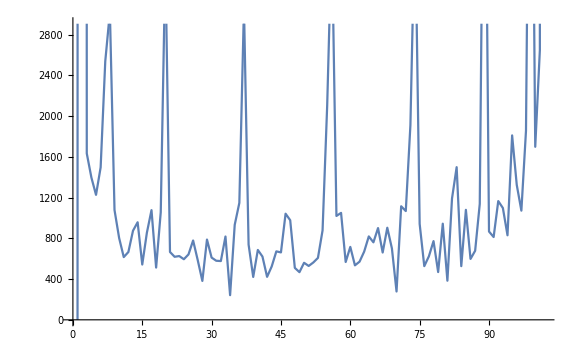

```mathematica
ListLinePlot[histo[[2]]]
```

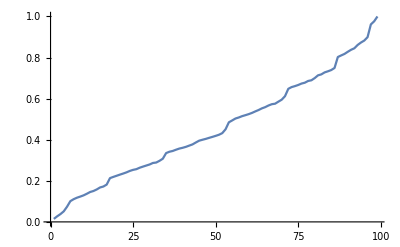

```mathematica
binCounts=Drop[Drop[histo[[2]],2],-1];
sumAO=Accumulate[binCounts];
sumAO/= sumAO[[-1]];
ListLinePlot[sumAO]
```

Converting AO into a cone aperture + ZH

The idea here is to use the AO value (i.e. a ratio of the visibility sphere we consider as unoccluded) into a set of ZH coefficients that will represent an occlusion cone.
From Sloan et al. (“Stupid SH Tricks”), they give the ZH coefficients for a smooth cone (Appendix A3) as, for the first 2 bands:

		Y_0(α)= ((α^3 +6α-12sin(α)+6cos(α)α)√π)/α^3
		Y_1(α)= 1/4((α^3 -3cos(α)sin(α)+3(cos(α))^2 α)√(3π))/α^3

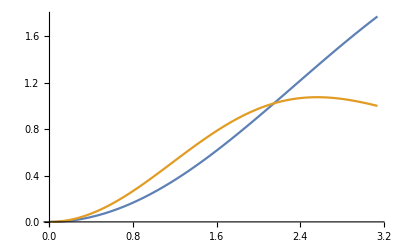

```mathematica
Y0[α_]:=((α^3 +6α-12Sin[α]+6Cos[α]α)√π)/α^3
Y1[α_]:=1/4((α^3 -3Cos[α]Sin[α]+3 Cos[α]^2 α)√(3π))/α^3
Plot[{Y0[α],Y1[α]},{α,0.01,π}]
```

We know that for ZH (i.e. m=0) we have:
	K_l=√((2l+1)/(4π))
So:
	K_0=√(1/(4π))	and 	K_1=√(3/(4π))

```mathematica
N[√(1/(4π))]
```

0.282095

// Builds a spherical harmonics cone lobe (same as for a spherical light source subtending a cone of half angle a)
		// (from “Stupid SH Tricks”)
		//
		void BuildSHCone( const in float3 _Direction, float _HalfAngle, out float _Coeffs[SH_COEFFS_COUNT] ) {
			float	a = _HalfAngle;
			float	c, s;
			sincos( a, s, c );
			float3 ZHCoeffs = float3(
					1.7724538509055160272981674833411 * (1 - c),			// sqrt(PI) (1 - cos(a))
					1.5349900619197327327193274373339 * (s * s),			// 0.5 sqrt(3PI) sin(a)^2
					1.9816636488030055066725143825601 * (c * (1 - c) * (1 + c))		// 0.5 sqrt(5PI) cos(a) (1-cos(a)) (cos(a)+1)
				);
			ZHRotate( _Direction, ZHCoeffs, _Coeffs );
		}

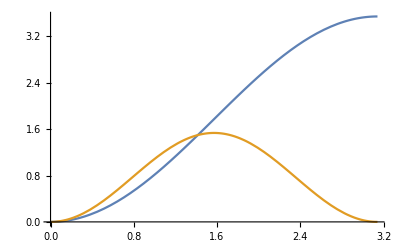

```mathematica
Y0[α_]:=(1-Cos[α])√π
Y1[α_]:=Sin[α]^2 √((3π)/4)
Plot[{Y0[α],Y1[α]},{α,0,π}]
```